## Utilities

```mathematica
init=<|"A"->9,"B"->2,"C"->2,"D"->4,"E"->12,"F"->2,"G"->3,"H"->2,"I"->9,"J"->1,"K"->1,"L"->4,"M"->2,"N"->6,"O"->8,"P"->2,"Q"->1,"R"->6,"S"->4,"T"->6,"U"->4,"V"->2,"W"->2,"X"->1,"Y"->2,"Z"->1,"?"->2|>;
Clear[editTileBag];
editTileBag[bingos_List]:=
Module[
{charCounts},
charCounts=Merge[Counts/@Characters/@bingos,Total];
Merge[
{
init,
AssociationMap[
(init[#]-charCounts[#])&,
Keys[charCounts]
]
},
Last
]
]
```

```mathematica
editTileBag[{"EARMUFF","TROUSES"}]
```

<|A→8,B→2,C→2,D→4,E→10,F→0,G→3,H→2,I→9,J→1,K→1,L→4,M→1,N→6,O→7,P→2,Q→1,R→4,S→2,T→5,U→2,V→2,W→2,X→1,Y→2,Z→1,?→2|>

```mathematica
CloudLoggingData[CloudObject[["https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays"](https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays)],"LastMonth"]
```

<|TotalCalls→677,TotalCredits→952,CallRateTimeSeries→TimeSeries[…]|>

```mathematica
%["CallRateTimeSeries"]
```

TimeSeries[…]

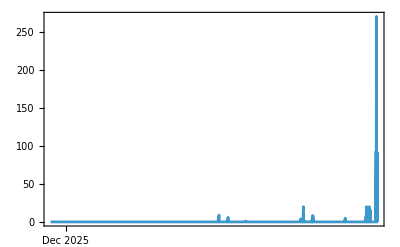

```mathematica
DateListPlot[%]
```

## UpdateTileBag

### Define Function

```mathematica
Clear[UpdateTileBag]
UpdateTileBag[tileBag_Association,bingo_String, blanksRemaining_Integer]:=
Module[
{
tilesInBingo=Characters[bingo],
charCounts,
newTileBag,
blanksNeeded
},
charCounts=Counts[tilesInBingo];
newTileBag=
Merge[
{
tileBag,
AssociationMap[
(tileBag[#]-charCounts[#])&,
tilesInBingo
]
},
Last
];
blanksNeeded=Abs[Total[Select[Values[newTileBag],#<0&]]];
If[
blanksNeeded<=blanksRemaining&&Min[Values[newTileBag]]>=-blanksRemaining,
newTileBag["?"]=newTileBag["?"]-blanksNeeded;
Return[
{
"success"->True,
"tileBag"->Normal[newTileBag]/.x_Integer/;x<0 :>0,
"blanks"->Flatten[KeyValueMap[Table[#1,-#2]&,Select[newTileBag,#<0&]]]
}
],
Return[
{
"success"->False,
"error"->"CANNOT-FORM-WORD"
}
]
]
]
```

```mathematica
CloudDeploy[
APIFunction[
{"tileBag"->"String","bingo"->"String","blanksRemaining"->"Integer"},
UpdateTileBag[
ImportString[URLDecode[#tileBag],"RawJSON"],
#bingo,
#blanksRemaining
]&,
"JSON"
],
"Scrabble/APIs/UpdateTileBag",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag]

### Test API

```mathematica
initialTileBag=URLEncode["{\"A\":9,\"B\":2,\"C\":2,\"D\":4,\"E\":12,\"F\":2,\"G\":3,\"H\":2,\"I\":9,\"J\":1,\"K\":1,\"L\":4,\"M\":2,\"N\":6,\"O\":8,\"P\":2,\"Q\":1,\"R\":6,\"S\":4,\"T\":6,\"U\":4,\"V\":2,\"W\":2,\"X\":1,\"Y\":2,\"Z\":1,\"?\":2}"
]
```

%7B%22A%22%3A9%2C%22B%22%3A2%2C%22C%22%3A2%2C%22D%22%3A4%2C%22E%22%3A12%2C%22F%22%3A2%2C%22G%22%3A3%2C%22H%22%3A2%2C%22I%22%3A9%2C%22J%22%3A1%2C%22K%22%3A1%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A6%2C%22O%22%3A8%2C%22P%22%3A2%2C%22Q%22%3A1%2C%22R%22%3A6%2C%22S%22%3A4%2C%22T%22%3A6%2C%22U%22%3A4%2C%22V%22%3A2%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D

```mathematica
ImportString[URLDecode[initialTileBag],"JSON"]
```

{A→9,B→2,C→2,D→4,E→12,F→2,G→3,H→2,I→9,J→1,K→1,L→4,M→2,N→6,O→8,P→2,Q→1,R→6,S→4,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2}

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"ENJAMBS","blanksRemaining"->2}
]
```

{success→True,tileBag→{A→8,B→1,C→2,D→4,E→11,F→2,G→3,H→2,I→9,J→0,K→1,L→4,M→1,N→5,O→8,P→2,Q→1,R→6,S→3,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2},blanks→{}}

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"COZZIES","blanksRemaining"->2}
]
```

{success→True,tileBag→{A→9,B→2,C→1,D→4,E→11,F→2,G→3,H→2,I→8,J→1,K→1,L→4,M→2,N→6,O→7,P→2,Q→1,R→6,S→3,T→6,U→4,V→2,W→2,X→1,Y→2,Z→0,?→1},blanks→{Z}}

```mathematica
URLExecute[
"https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/UpdateTileBag",
{"tileBag"->initialTileBag,"bingo"->"ZYZZYVAZ","blanksRemaining"->2}
]
```

{success→False,error→CANNOT-FORM-WORD}

## Battleship

```mathematica
(* Identify squares used up by a 'bingo' placed at '(row, col)'. *)
Clear[Battleship];
Battleship[spot_/;spot["direction"]=="H"]:=
Module[
{row,col,length=StringLength[spot["bingo"]]},
{row,col}={spot["row"],spot["col"]};
Table[
{row,col+i},
{i,0,length-1}
]
];
Battleship[spot_/;spot["direction"]=="V"]:=
Module[
{row,col,length=StringLength[spot["bingo"]]},
{row,col}={spot["row"],spot["col"]};
Table[
{row+i,col},
{i,0,length-1}
]
];

(* Identify squares in the 'forbidden zones' around already played words. *)
Clear[ForbiddenSquares];
ForbiddenSquares[turn_Association/;turn["direction"]=="H"]:=
Module[
{row,col,length=StringLength[turn["bingo"]]},
{row,col}={turn["row"],turn["col"]};
Join[
Table[{row,col+i},{i,-1,length}],
Table[{row-1,col+i},{i,0,length-1}],
Table[{row+1,col+i},{i,0,length-1}]
]
];
ForbiddenSquares[turn_Association/;turn["direction"]=="V"]:=
Module[
{row,col,length=StringLength[turn["bingo"]]},
{row,col}={turn["row"],turn["col"]};
Join[
Table[{row+i,col},{i,-1,length}],
Table[{row+i,col-1},{i,0,length-1}],
Table[{row+i,col+1},{i,0,length-1}]
]
];
```

## FindViablePlays

### FindBingoSpots

#### Vertically

Find spots to play the next bingo through previous horizontal turns.

```mathematica
Clear[FindBingoSpots]
FindBingoSpots[bingo_String,turn_Association/;turn["direction"]=="H"]:=
Module[
{
word=turn["bingo"],row=turn["row"],col=turn["col"],id=turn["id"],overlaps,startingPosList
},
overlaps=Intersection[Characters[word],Characters[bingo]];
Flatten[
Map[
With[
{
toTile=StringPosition[word,#][[All,1]]-1,
retrace=StringPosition[bingo,#][[All,1]]-1
},
startingPosList=
Flatten[
Outer[List,(row-retrace),(col+toTile)],
1
];
Table[
<|"bingo"->bingo,"row"->pos[[1]],"col"->pos[[2]],"direction"->"V","playThroughTurn"->id,"overlapTile"->#|>,
{pos,startingPosList}
]
]&,
overlaps
],
1
]
];
```

#### Horizontally

Find spots to play the next bingo through previous vertical turns.

```mathematica
FindBingoSpots[bingo_String,turn_Association/;turn["direction"]=="V"]:=
Module[
{
word=turn["bingo"],row=turn["row"],col=turn["col"],id=turn["id"],overlaps,startingPosList
},
overlaps=Intersection[Characters[word],Characters[bingo]];
Flatten[
Map[
With[
{
toTile=StringPosition[word,#][[All,1]]-1,
retrace=StringPosition[bingo,#][[All,1]]-1
},
startingPosList=
Flatten[
Outer[List,(row+toTile),(col-retrace)],
1
];
Table[
<|"bingo"->bingo,"row"->pos[[1]],"col"->pos[[2]],"direction"->"H","playThroughTurn"->id,"overlapTile"->#|>,
{pos,startingPosList}
]
]&,
overlaps
],
1
]
];
```

### FindViablePlays

Find all possible locations to play a bingo given a set of previous turns.

Check tile bag

Battleship

All turns except turn to be played through must have forbidden cushion. Turn to be played through can have Battleship.

```mathematica
Flatten[KeyValueMap[Table[#1,-#2]&,Select[<|"A"->4,"B"->-1,"C"->3,"D"->-1|>,#<0&]]]
```

{B,D}

```mathematica
Flatten[KeyValueMap[Table[#1,-#2]&,Select[<|"A"->4,"B"->1,"C"->3,"D"->1,"Z"->-2|>,#<0&]]]
```

{Z,Z}

```mathematica
Clear[FindViablePlays];
FindViablePlays[bingo_String,turns_List]:=
Module[
{plays={},spots,avoidCols,playDown,avoidRows,playAcross,playsWithTileBag,playsWithForbiddenSquares,validPlays},
plays=
Flatten[
Map[
If[
#["direction"]==="H",
spots=FindBingoSpots[bingo,#];
avoidCols=Select[turns,#["direction"]=="V" &][[All,"col"]];
playDown=
Select[
spots,
!MemberQ[avoidCols,#["col"]]&&#["row"]<=7&&#["row"]>=0 &
];
Join[plays,playDown],
spots=FindBingoSpots[bingo,#];
avoidRows=Select[turns,#["direction"]=="H" &][[All,"row"]];
playAcross=
Select[
spots,
!MemberQ[avoidRows,#["row"]]&&#["col"]<=7&&#["col"]>=0 &
];
Join[plays,playAcross]
]&,
turns
],
1
];
Echo[plays];
playsWithTileBag=
Map[
Join[
#,
With[
{possibleBingo=#["bingo"],overlapTile=#["overlapTile"]},
{response=
Enclose[
ConfirmMatch[
UpdateTileBag[Last[turns]["tileBag"],StringJoin[DeleteElements[Characters[possibleBingo],1->{overlapTile}]], Last[turns]["tileBag"]["?"]],
    {"success"->True,"tileBag"->_List,"blanks"->_List}
]
]
},
<|
"tileBag"->If[FailureQ[response],$Failed,Association[response]["tileBag"]],
"tilesLeft"->If[FailureQ[response],$Failed,Total[Values[Association[response]["tileBag"]]]],
"blanks"->If[FailureQ[response],$Failed,Association[response]["blanks"]]
|>
]
]&,
plays
];
Echo[playsWithTileBag];
playsWithForbiddenSquares=
Map[
With[
{play=#,playThroughTurn=#["playThroughTurn"]},
Append[
play,
"forbiddenSquares"->
Flatten[
Map[
With[
{turn=#},
If[
turn["id"]==playThroughTurn,
Battleship[turn],
ForbiddenSquares[turn]
]
]&,
turns
],
1
]
]
]&,
playsWithTileBag
];
Echo[playsWithForbiddenSquares];
validPlays=
Select[
playsWithForbiddenSquares,
ListQ[#["tileBag"]]&&
Length[Intersection[Battleship[#],#["forbiddenSquares"]]]==1
&
];
Echo[validPlays];
If[
Length[validPlays]>0,
  Return[
{
"success"->True,
"viablePlays"->
Normal[KeyDrop[validPlays,{"forbiddenSquares","playThroughTurn"}]]
}
],
Return[
{
"success"->False,
"error"->
"NO-VIABLE-PLAYS"
}
]
]
];
```

### Deploy API

```mathematica
CloudDeploy[
APIFunction[
{"bingo"->"String","turns"->"String"},
FindViablePlays[
#bingo,
ImportString[URLDecode[#turns],"RawJSON"]
]&,
"JSON"
],
"Scrabble/APIs/FindViablePlays",
Permissions->"Public"
]
```

CloudObject[https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays]

### Test API

```mathematica
URLDecode["https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays?bingo=CEPHALIN&turns=%5B%7B%22id%22%3A1%2C%22bingo%22%3A%22OREGANO%22%2C%22row%22%3A7%2C%22col%22%3A7%2C%22direction%22%3A%22H%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A8%2C%22B%22%3A2%2C%22C%22%3A2%2C%22D%22%3A4%2C%22E%22%3A11%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A2%2C%22I%22%3A9%2C%22J%22%3A1%2C%22K%22%3A1%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A6%2C%22P%22%3A2%2C%22Q%22%3A1%2C%22R%22%3A5%2C%22S%22%3A4%2C%22T%22%3A6%2C%22U%22%3A4%2C%22V%22%3A2%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A93%7D%2C%7B%22id%22%3A2%2C%22bingo%22%3A%22KVETCHES%22%2C%22row%22%3A5%2C%22col%22%3A9%2C%22direction%22%3A%22V%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A8%2C%22B%22%3A2%2C%22C%22%3A1%2C%22D%22%3A4%2C%22E%22%3A10%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A9%2C%22J%22%3A1%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A6%2C%22P%22%3A2%2C%22Q%22%3A1%2C%22R%22%3A5%2C%22S%22%3A3%2C%22T%22%3A5%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A86%7D%2C%7B%22id%22%3A3%2C%22bingo%22%3A%22APRICOTS%22%2C%22row%22%3A12%2C%22col%22%3A2%2C%22direction%22%3A%22H%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A7%2C%22B%22%3A2%2C%22C%22%3A0%2C%22D%22%3A4%2C%22E%22%3A10%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A8%2C%22J%22%3A1%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A5%2C%22P%22%3A1%2C%22Q%22%3A1%2C%22R%22%3A4%2C%22S%22%3A3%2C%22T%22%3A4%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A79%7D%2C%7B%22id%22%3A4%2C%22bingo%22%3A%22JETPORTS%22%2C%22row%22%3A7%2C%22col%22%3A4%2C%22direction%22%3A%22V%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A7%2C%22B%22%3A2%2C%22C%22%3A0%2C%22D%22%3A4%2C%22E%22%3A9%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A8%2C%22J%22%3A0%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A4%2C%22P%22%3A0%2C%22Q%22%3A1%2C%22R%22%3A4%2C%22S%22%3A2%2C%22T%22%3A2%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A72%7D%5D"]
```

https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays?bingo=CEPHALIN&turns=[{"id":1,"bingo":"OREGANO","row":7,"col":7,"direction":"H","score":0,"blanksUsed":0,"tileBag":{"A":8,"B":2,"C":2,"D":4,"E":11,"F":2,"G":2,"H":2,"I":9,"J":1,"K":1,"L":4,"M":2,"N":5,"O":6,"P":2,"Q":1,"R":5,"S":4,"T":6,"U":4,"V":2,"W":2,"X":1,"Y":2,"Z":1,"?":2},"tilesLeft":93},{"id":2,"bingo":"KVETCHES","row":5,"col":9,"direction":"V","score":0,"blanksUsed":0,"tileBag":{"A":8,"B":2,"C":1,"D":4,"E":10,"F":2,"G":2,"H":1,"I":9,"J":1,"K":0,"L":4,"M":2,"N":5,"O":6,"P":2,"Q":1,"R":5,"S":3,"T":5,"U":4,"V":1,"W":2,"X":1,"Y":2,"Z":1,"?":2},"tilesLeft":86},{"id":3,"bingo":"APRICOTS","row":12,"col":2,"direction":"H","score":0,"blanksUsed":0,"tileBag":{"A":7,"B":2,"C":0,"D":4,"E":10,"F":2,"G":2,"H":1,"I":8,"J":1,"K":0,"L":4,"M":2,"N":5,"O":5,"P":1,"Q":1,"R":4,"S":3,"T":4,"U":4,"V":1,"W":2,"X":1,"Y":2,"Z":1,"?":2},"tilesLeft":79},{"id":4,"bingo":"JETPORTS","row":7,"col":4,"direction":"V","score":0,"blanksUsed":0,"tileBag":{"A":7,"B":2,"C":0,"D":4,"E":9,"F":2,"G":2,"H":1,"I":8,"J":0,"K":0,"L":4,"M":2,"N":5,"O":4,"P":0,"Q":1,"R":4,"S":2,"T":2,"U":4,"V":1,"W":2,"X":1,"Y":2,"Z":1,"?":2},"tilesLeft":72}]

```mathematica
URLExecute["https://www.wolframcloud.com/obj/josephb/Scrabble/APIs/FindViablePlays?bingo=CEPHALIN&turns=%5B%7B%22id%22%3A1%2C%22bingo%22%3A%22OREGANO%22%2C%22row%22%3A7%2C%22col%22%3A7%2C%22direction%22%3A%22H%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A8%2C%22B%22%3A2%2C%22C%22%3A2%2C%22D%22%3A4%2C%22E%22%3A11%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A2%2C%22I%22%3A9%2C%22J%22%3A1%2C%22K%22%3A1%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A6%2C%22P%22%3A2%2C%22Q%22%3A1%2C%22R%22%3A5%2C%22S%22%3A4%2C%22T%22%3A6%2C%22U%22%3A4%2C%22V%22%3A2%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A93%7D%2C%7B%22id%22%3A2%2C%22bingo%22%3A%22KVETCHES%22%2C%22row%22%3A5%2C%22col%22%3A9%2C%22direction%22%3A%22V%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A8%2C%22B%22%3A2%2C%22C%22%3A1%2C%22D%22%3A4%2C%22E%22%3A10%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A9%2C%22J%22%3A1%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A6%2C%22P%22%3A2%2C%22Q%22%3A1%2C%22R%22%3A5%2C%22S%22%3A3%2C%22T%22%3A5%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A86%7D%2C%7B%22id%22%3A3%2C%22bingo%22%3A%22APRICOTS%22%2C%22row%22%3A12%2C%22col%22%3A2%2C%22direction%22%3A%22H%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A7%2C%22B%22%3A2%2C%22C%22%3A0%2C%22D%22%3A4%2C%22E%22%3A10%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A8%2C%22J%22%3A1%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A5%2C%22P%22%3A1%2C%22Q%22%3A1%2C%22R%22%3A4%2C%22S%22%3A3%2C%22T%22%3A4%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A79%7D%2C%7B%22id%22%3A4%2C%22bingo%22%3A%22JETPORTS%22%2C%22row%22%3A7%2C%22col%22%3A4%2C%22direction%22%3A%22V%22%2C%22score%22%3A0%2C%22blanksUsed%22%3A0%2C%22tileBag%22%3A%7B%22A%22%3A7%2C%22B%22%3A2%2C%22C%22%3A0%2C%22D%22%3A4%2C%22E%22%3A9%2C%22F%22%3A2%2C%22G%22%3A2%2C%22H%22%3A1%2C%22I%22%3A8%2C%22J%22%3A0%2C%22K%22%3A0%2C%22L%22%3A4%2C%22M%22%3A2%2C%22N%22%3A5%2C%22O%22%3A4%2C%22P%22%3A0%2C%22Q%22%3A1%2C%22R%22%3A4%2C%22S%22%3A2%2C%22T%22%3A2%2C%22U%22%3A4%2C%22V%22%3A1%2C%22W%22%3A2%2C%22X%22%3A1%2C%22Y%22%3A2%2C%22Z%22%3A1%2C%22%3F%22%3A2%7D%2C%22tilesLeft%22%3A72%7D%5D"
]
```

{success→True,viablePlays→{{bingo→CEPHALIN,row→3,col→11,direction→V,overlapTile→A,tileBag→{A→7,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}},{bingo→CEPHALIN,row→0,col→12,direction→V,overlapTile→N,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→5,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}},{bingo→CEPHALIN,row→10,col→6,direction→H,overlapTile→H,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→1,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}}}}

```mathematica
Dataset[Values[%77][[2]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\josephb\PersonalProjects\scrabble

#### Standard

```mathematica
turnsAssoc=;
```

```mathematica
FindViablePlays[
"CEPHALIN",
turnsAssoc
]
```

{<|bingo→CEPHALIN,row→3,col→11,direction→V,playThroughTurn→1,overlapTile→A|>,<|bingo→CEPHALIN,row→0,col→12,direction→V,playThroughTurn→1,overlapTile→N|>,<|bingo→CEPHALIN,row→10,col→6,direction→H,playThroughTurn→2,overlapTile→H|>,<|bingo→CEPHALIN,row→6,col→5,direction→V,playThroughTurn→3,overlapTile→I|>,<|bingo→CEPHALIN,row→8,col→3,direction→H,playThroughTurn→4,overlapTile→E|>,<|bingo→CEPHALIN,row→10,col→2,direction→H,playThroughTurn→4,overlapTile→P|>}

{<|bingo→CEPHALIN,row→3,col→11,direction→V,playThroughTurn→1,overlapTile→A,tileBag→{A→7,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}|>,<|bingo→CEPHALIN,row→0,col→12,direction→V,playThroughTurn→1,overlapTile→N,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→5,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}|>,<|bingo→CEPHALIN,row→10,col→6,direction→H,playThroughTurn→2,overlapTile→H,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→1,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}|>,<|bingo→CEPHALIN,row→6,col→5,direction→V,playThroughTurn→3,overlapTile→I,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→8,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}|>,<|bingo→CEPHALIN,row→8,col→3,direction→H,playThroughTurn→4,overlapTile→E,tileBag→{A→6,B→2,C→0,D→4,E→9,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P}|>,<|bingo→CEPHALIN,row→10,col→2,direction→H,playThroughTurn→4,overlapTile→P,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→1},tilesLeft→65,blanks→{C}|>}

{<|bingo→CEPHALIN,row→3,col→11,direction→V,playThroughTurn→1,overlapTile→A,tileBag→{A→7,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→0,col→12,direction→V,playThroughTurn→1,overlapTile→N,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→5,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→10,col→6,direction→H,playThroughTurn→2,overlapTile→H,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→1,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→6,col→5,direction→V,playThroughTurn→3,overlapTile→I,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→8,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→8,col→3,direction→H,playThroughTurn→4,overlapTile→E,tileBag→{A→6,B→2,C→0,D→4,E→9,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4}}|>,<|bingo→CEPHALIN,row→10,col→2,direction→H,playThroughTurn→4,overlapTile→P,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→1},tilesLeft→65,blanks→{C},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4}}|>}

{<|bingo→CEPHALIN,row→3,col→11,direction→V,playThroughTurn→1,overlapTile→A,tileBag→{A→7,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→0,col→12,direction→V,playThroughTurn→1,overlapTile→N,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→5,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>,<|bingo→CEPHALIN,row→10,col→6,direction→H,playThroughTurn→2,overlapTile→H,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→1,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}|>}

{success→True,viablePlays→{{bingo→CEPHALIN,row→3,col→11,direction→V,playThroughTurn→1,overlapTile→A,tileBag→{A→7,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}},{bingo→CEPHALIN,row→0,col→12,direction→V,playThroughTurn→1,overlapTile→N,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→0,I→7,J→0,K→0,L→3,M→2,N→5,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{4,9},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{13,9},{5,8},{6,8},{7,8},{8,8},{9,8},{10,8},{11,8},{12,8},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{11,10},{12,10},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}},{bingo→CEPHALIN,row→10,col→6,direction→H,playThroughTurn→2,overlapTile→H,tileBag→{A→6,B→2,C→0,D→4,E→8,F→2,G→2,H→1,I→7,J→0,K→0,L→3,M→2,N→4,O→4,P→0,Q→1,R→4,S→2,T→2,U→4,V→1,W→2,X→1,Y→2,Z→1,?→0},tilesLeft→65,blanks→{C,P},forbiddenSquares→{{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12},{8,13},{5,9},{6,9},{7,9},{8,9},{9,9},{10,9},{11,9},{12,9},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{6,4},{7,4},{8,4},{9,4},{10,4},{11,4},{12,4},{13,4},{14,4},{15,4},{7,3},{8,3},{9,3},{10,3},{11,3},{12,3},{13,3},{14,3},{7,5},{8,5},{9,5},{10,5},{11,5},{12,5},{13,5},{14,5}}}}}

```mathematica
Dataset[Values[][[2]]]
```

## To Do:

Remove Echoes

Better error messages.

One for tile bag issues

One for board space issues

Blank styling

OK for first turn

Not subsequent turns

Blank tile registered as having ‘-1’ then total is out of whack.

Blanks used is always zero?